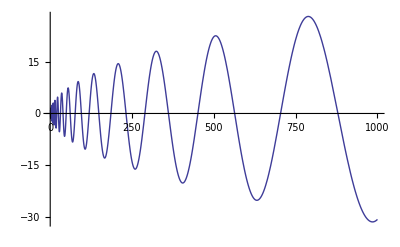

```mathematica
Plot[Re[x^(1-N[ZetaZero[1]])],{x,1,1000}]
```

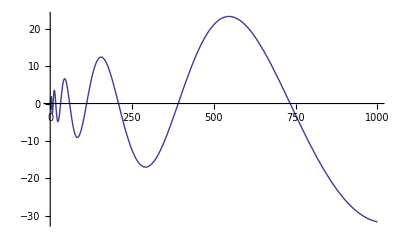

```mathematica
Plot[Re[x^(1-(.5+5I))],{x,1,1000}]
```

```mathematica
FullSimplify[(1-x^(1-s))Zeta[s]]/.s->3
```

(1-1/x^2) Zeta[3]

```mathematica
FullSimplify[(x^(s-1)-1)/x^(s-1) zZeta[s]/.s->ZetaZero[1]]
```

(1-x^(1-ZetaZero[1])) zZeta[ZetaZero[1]]

```mathematica
par[n_,s_]:=Sum[ j^-s,{j,1,n}]
```

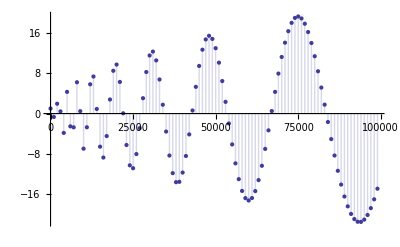

```mathematica
DiscretePlot[Re[par[n,N[ZetaZero[1]]]],{n,1,100000,1000}]
```

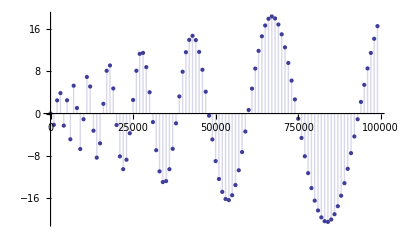

```mathematica
DiscretePlot[Im[par[n,N[ZetaZero[1]]]],{n,1,100000,1000}]
```

```mathematica
DiscretePlot[{ Re[par[n,N[ZetaZero[1]]]] ,Re[n^(1-N[ZetaZero[1]])]},{n,1,1000,1}]
```

```mathematica
f[x_]:=Sum[ j^-s,{j,1,n}]-x^(1-s)Sum[ j^-s,{j,1,n/x}]
f2[x_]:=-x^(1-s)Sum[ j^-s,{j,1,n/x}]
f3[x_]:=Sum[(-x^(1-s))( j^-s),{j,1,n/x}]
f4[x_]:=Sum[(-x^(1-s))( j^-s),{j,1,n/x}]
f5[n_,s_,x_]:=Sum[-j^-s (1-s) x^-s,{j,1,n/x}]
f6[x_]:=Sum[-j^-s x^(1-s),{j,1,n/x}]
```

```mathematica
FullSimplify@D[f[x],x]
```

x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])

```mathematica
N[x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])/.s->N[ZetaZero[1]]/.n->1000000000000000000/.x->2]
```

1.14871×10^-7-1.67402×10^-6 ⅈ

```mathematica
Limit[x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x]),n->Infinity]
```

Limit[x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x]),n→∞]

```mathematica
D[f[x],x]
```

-(1-s) x^-s HarmonicNumber[n/x,s]+n s x^(-1-s) (-HarmonicNumber[n/x,1+s]+Zeta[1+s])

```mathematica
N[-(1-s) x^-s HarmonicNumber[n/x,s]+n s x^(-1-s) (-HarmonicNumber[n/x,1+s]+Zeta[1+s])]/.s->N[ZetaZero[1]]/.n->10000000000000000/.x->2
```

-0.0526776-0.550533 ⅈ

```mathematica
FullSimplify@D[f2[x],x]
```

x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])

```mathematica
FullSimplify@D[f3[x],x]
```

x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])

```mathematica
x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])/.s->N[ZetaZero[1]]/.n->10000000000000000/.x->2
```

-4.42509×10^-8-3.36104×10^-8 ⅈ

```mathematica
FullSimplify@D[f4[x],x]
```

```mathematica
x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])/.s->N[ZetaZero[1]]/.n->10000000000000000/.x->4
```

1.07906×10^-8+1.03187×10^-8 ⅈ

```mathematica
FullSimplify@D[f4[x],{x,2}]
```

```mathematica
s x^(-3-s) ((-1+s) x^2 HurwitzZeta[s,(n+x)/x]-2 n s x HurwitzZeta[1+s,(n+x)/x]+n^2 (1+s) HurwitzZeta[2+s,(n+x)/x]-(-1+s) x^2 Zeta[s])/.s->N[ZetaZero[12]]/.n->10000000000000/.x->2
```

-1.66366×10^-7+2.9153×10^-7 ⅈ

```mathematica
D[(-x^(1-s))( j^-s),x]
```

-j^-s (1-s) x^-s

```mathematica
f5[10000000000000000,N[ZetaZero[1]],2]
```

-3.61776×10^7-3.45135×10^7 ⅈ

```mathematica
N[x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])/.s->N@ZetaZero[1]/.n->10000000000000000/.x->5]
```

3.90634×10^-9+3.64325×10^-9 ⅈ

```mathematica
N[ ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])/.s->N@ZetaZero[1]/.n->10000000000000000/.x->5]
```

-3.72529×10^-9-5.96046×10^-8 ⅈ

```mathematica
FullSimplify[(-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x]]
```

(-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x]

```mathematica
FullSimplify[(-x^(1-s))( j^-s)]
```

-j^-s x^(1-s)

```mathematica
FullSimplify@D[f6[x],x]
```

```mathematica
N[((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])/.s->2/.n->10000000000/.x->2]
```

3.28987

```mathematica
Pi^2/3.
```

3.28987

```mathematica
FullSimplify[D[Sum[-j^-s x^(1-s),{j,1,n/x}],x]]
```

x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])

```mathematica
FullSimplify[Sum[D[-j^-s x^(1-s),x],{j,1,n/x}]]
```

(-1+s) x^-s HarmonicNumber[n/x,s]

```mathematica
N[(-1+s) x^-s HarmonicNumber[n/x,s]/.s->N@ZetaZero[1]/.n->10000000000/.x->3]
```

-10144.3-31752.2 ⅈ

```mathematica
N[x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])/.s->N@ZetaZero[2]/.n->100000000000/.x->2]
```

7.04541×10^-8-1.57978×10^-6 ⅈ

```mathematica
N[ ((-1+s) x HarmonicNumber[n/x,s])/.s->N@ZetaZero[12]/.n->1000000000/.x->4]
```

12810.6-61934.5 ⅈ

```mathematica
N[ (n s HurwitzZeta[1+s,(n+x)/x])/.s->N@ZetaZero[12]/.n->1000000000/.x->4]
```

-12810.6+61934.5 ⅈ

```mathematica
N[ x^(-1-s)(Sum[ ((-1+s) x )/j^s,{j,1,n/x}]+(Sum[(n s)/(j+(n/x)+1)^(s+1),{j,0,Infinity}]))/.s->N[ZetaZero[3]]/.n->100000000000/.x->1]
```

-6.94563×10^-7-1.41968×10^-6 ⅈ

```mathematica
FullSimplify[D[f6[x],{x,2}]/.x->1]
```

s ((-1+s) HurwitzZeta[s,1+n]-2 n s HurwitzZeta[1+s,1+n]+n^2 (1+s) HurwitzZeta[2+s,1+n]+Zeta[s]-s Zeta[s])

```mathematica
FullSimplify[D[f6[x],{x,3}]/.x->1]
```

s (1+s) (-(-1+s) HurwitzZeta[s,1+n]+3 n s HurwitzZeta[1+s,1+n]-3 n^2 (1+s) HurwitzZeta[2+s,1+n]+n^3 (2+s) HurwitzZeta[3+s,1+n]+(-1+s) Zeta[s])

```mathematica
fr[s_]:=N[x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])/.n->100000000000000/.x->1]
fr2[s_]:=N[s ((-1+s) HurwitzZeta[s,1+n]-2 n s HurwitzZeta[1+s,1+n]+n^2 (1+s) HurwitzZeta[2+s,1+n]+Zeta[s]-s Zeta[s])/.n->100000000000000/.x->1]
fr3[s_]:=N[s (1+s) (-(-1+s) HurwitzZeta[s,1+n]+3 n s HurwitzZeta[1+s,1+n]-3 n^2 (1+s) HurwitzZeta[2+s,1+n]+n^3 (2+s) HurwitzZeta[3+s,1+n]+(-1+s) Zeta[s])/.n->100000000000000/.x->1]
```

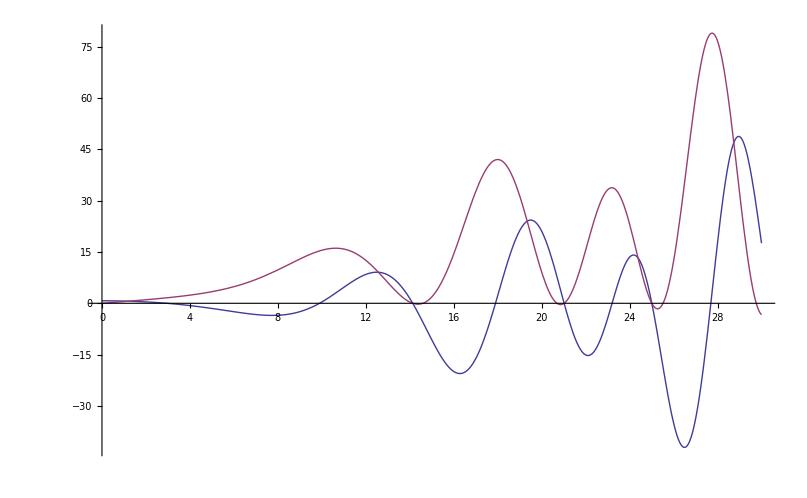

```mathematica
Plot[{Re[ fr[.5+t I]],Im[ fr[.5+t I]]},{t,0,30}]
```

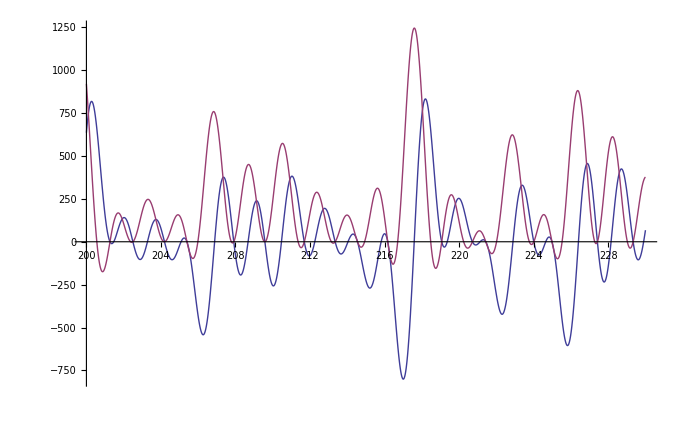

```mathematica
Plot[{Re[fr[.5+t I]],Im[fr[.5+t I]]},{t,200,200+30}]
```

```mathematica
FullSimplify[D[f4[x],{x,0}]/.x->1]
```

-HarmonicNumber[n,s]

```mathematica
D[(1-x^(1-s))Zeta[s],x]
```

-(1-s) x^-s Zeta[s]

```mathematica
f6[x_]:=Sum[-j^-s x^(1-s),{j,1,n/x}]
f6a[x_]:=Sum[D[-j^-s x^(1-s),{x,2}],{j,1,n/x}]
```

```mathematica
D[f6[x],x]
```

-(1-s) x^-s HarmonicNumber[n/x,s]+n s x^(-1-s) (-HarmonicNumber[n/x,1+s]+Zeta[1+s])

```mathematica
-(1-s) x^-s HarmonicNumber[n/x,s]+n s x^(-1-s) (-HarmonicNumber[n/x,1+s]+Zeta[1+s])/.x->1
```

(-1+s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])

```mathematica
N[(-1+s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])/.n->100000/.s->N[ZetaZero[1]]]
```

-0.00127692-0.000932455 ⅈ

```mathematica
FullSimplify[D[f6[x],x]/.x->1]
```

```mathematica
N[(-1+s) HarmonicNumber[n,s]+n s HurwitzZeta[1+s,1+n]/.n->100000000000/.s->N[ZetaZero[1]]]
```

-1.56701×10^-6-2.06586×10^-7 ⅈ

```mathematica
Expand[(-1+s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])]
```

-HarmonicNumber[n,s]+s HarmonicNumber[n,s]-n s HarmonicNumber[n,1+s]+n s Zeta[1+s]

```mathematica
fr2[n_,s_]:=Sum[ (s-1)/j^s-n s/j^(s+1),{j,1,n}]+n s Zeta[1+s]
```

```mathematica
fr2[100000000000,N@ZetaZero[1]]
```

-0.0000305176+0.00012207 ⅈ

```mathematica
N[1-ZetaZero[1]]
```

0.5-14.1347 ⅈ

```mathematica
N[ZetaZero[1]]
```

0.5+14.1347 ⅈ

```mathematica
Table[N[2^k/((2^k+3)^1.5)],{k,1,30}]
```

{0.178885,0.21598,0.219281,0.193192,0.154542,0.116699,0.0853696,0.0614172,0.0438086,0.0311132,0.0220486,0.0156078,0.0110425,0.00781035,0.00552351,0.00390598,0.00276204,0.00195309,0.00138106,0.000976558,0.000690532,0.000488281,0.000345267,0.000244141,0.000172633,0.00012207,0.0000863167,0.0000610352,0.0000431584,0.0000305176}

```mathematica
f6[x_]:=Sum[-j^-s x^(1-s),{j,1,n/x}]
f6b[x_]:=Sum[-j^-s x^(1-s),{j,1,n}]
```

```mathematica
D[f6[x],x]/.x->1
```

-(1-s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])

```mathematica
D[f6b[x],x]
```

-(1-s) x^-s HarmonicNumber[n,s]

```mathematica
N[x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])/.s->N@ZetaZero[2]/.n->100000000000/.x->2]
```

```mathematica
x^(-1-s) ((-1+s) x HarmonicNumber[n/x,s]+n s HurwitzZeta[1+s,(n+x)/x])/.x->1
```

(-1+s) HarmonicNumber[n,s]+n s HurwitzZeta[1+s,1+n]

```mathematica
N[(-1+s) HarmonicNumber[n,s]+n s HurwitzZeta[1+s,1+n]/.s->N@ZetaZero[2]/.n->100000000000]
```

7.04204×10^-8-1.579×10^-6 ⅈ

```mathematica
N[n (s) HurwitzZeta[1+s,1+n]-(1-s) HarmonicNumber[n,s]/.s->N@ZetaZero[2]/.n->100000000000]
```

7.04204×10^-8-1.579×10^-6 ⅈ

```mathematica
N[ (s) (n HurwitzZeta[1+s,1+n])-(1-s) HarmonicNumber[n,s]/.s->N@ZetaZero[2]/.n->100000000000]
```

7.04204×10^-8-1.579×10^-6 ⅈ

```mathematica
N[ (s) (n HurwitzZeta[1+s,1+n])-(1-s) HarmonicNumber[n,s]/.s->N@ZetaZero[2]]
```

(-0.5+21.022 ⅈ) HarmonicNumber[n,0.5+21.022 ⅈ]+(0.5+21.022 ⅈ) n HurwitzZeta[1.5+21.022 ⅈ,1.+n]

```mathematica
N[ {(s) (n HurwitzZeta[1+s,1+n]),(1-s) HarmonicNumber[n,s]}/.s->N@ZetaZero[2]]/.n->100000000000
```

{-14089.2+315914. ⅈ,-14089.2+315914. ⅈ}

```mathematica
N[ { (s)(n HurwitzZeta[1+s,1+n]), (1-s)HarmonicNumber[n,s]}/.s->N@ZetaZero[1]]/.n->100000000000
```

{313515.+41332.9 ⅈ,313515.+41332.9 ⅈ}

```mathematica
N@ZetaZero[1]
```

0.5+14.1347 ⅈ

```mathematica
N[ { Abs[(s)(n HurwitzZeta[1+s,1+n])], Abs[(1-s)HarmonicNumber[n,s]]}/.s->N@ZetaZero[1]]/.n->100000000000
```

{316228.,316228.}

```mathematica
N[ { Abs[(n HurwitzZeta[1+s,1+n])], Abs[HarmonicNumber[n,s]]}/.s->N@ZetaZero[1]]/.n->100000000000
```

{22358.4,22358.4}

```mathematica
N[ { Abs[(n HurwitzZeta[1+s,1+n])], Abs[HarmonicNumber[n,s]]}/.s->.2+N@ZetaZero[1]]/.n->100000000000
```

{140.988,141.133}

```mathematica
N[ { Abs[(n HurwitzZeta[1+s,1+n])], Abs[HarmonicNumber[n,s]]}/.s->13.2I+N@ZetaZero[1]]/.n->100000000000000000
```

{1.15668×10^7,1.15668×10^7}

```mathematica
N[ { Abs[(n HurwitzZeta[1+s,1+n])], Abs[HarmonicNumber[n,s]]}/.s->.3+N@ZetaZero[1]]/.n->100000000000000000
```

{177.426,177.797}

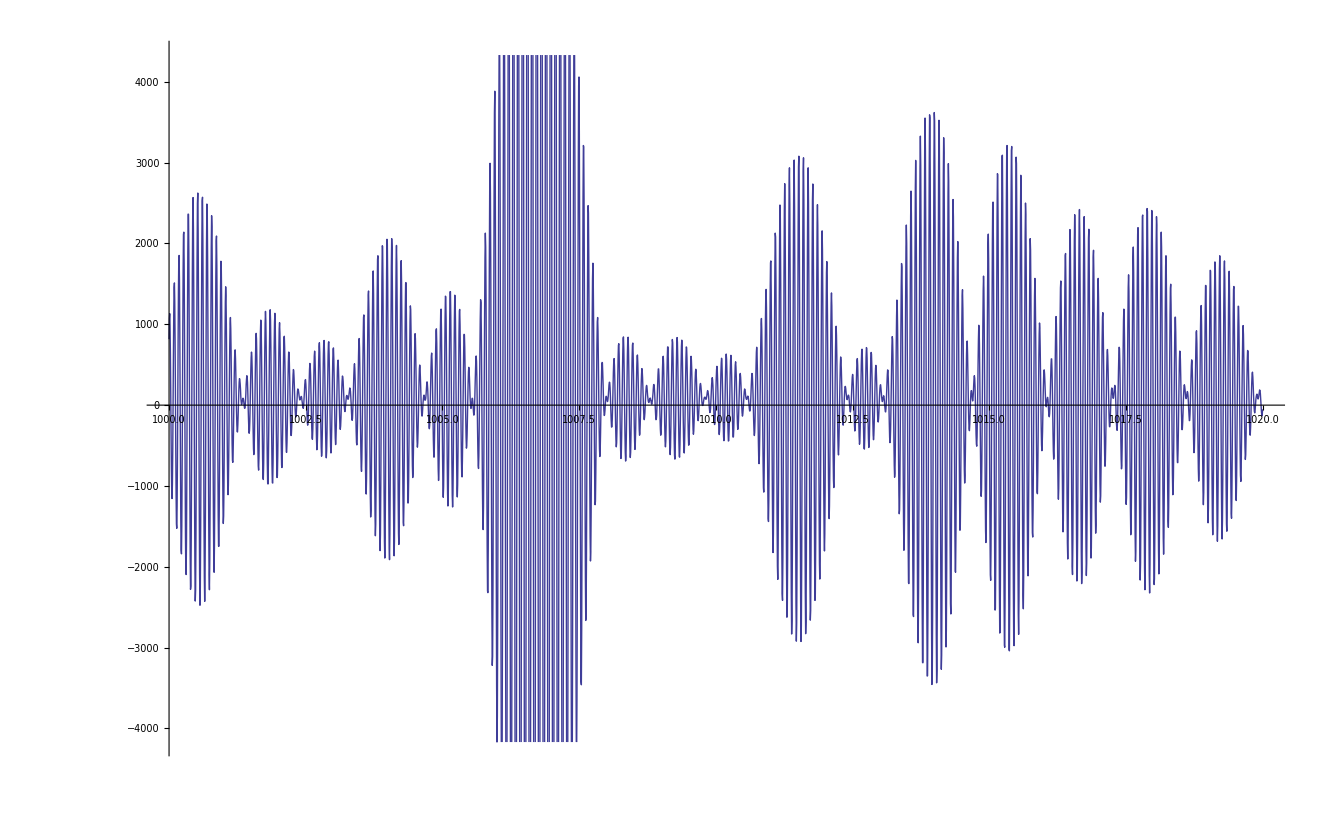

```mathematica
Plot[  { Abs[(s)(n HurwitzZeta[1+s,1+n])]- Abs[(1-s)HarmonicNumber[n,s]]}/.n->1000000000000000000000000000000000/.s->.5+t I,{t,1000,1020}]
```

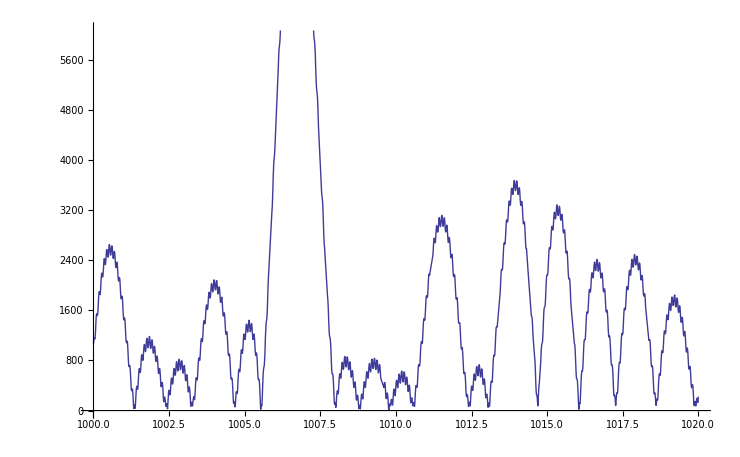

```mathematica
Plot[  { Abs[(s)(n HurwitzZeta[1+s,1+n])- (1-s)HarmonicNumber[n,s]]}/.n->1000000000000000000000000000000000/.s->.5+t I,{t,1000,1020}]
```

```mathematica
D[(1-x^(1-s))Zeta[s],x]/.x->1
```

```mathematica
-(1-s) Zeta[s]/.s->.3+N[ZetaZero[2]]
```

1.16198+5.90511 ⅈ

```mathematica
N[n (s) HurwitzZeta[1+s,1+n]-(1-s) HarmonicNumber[n,s]/.s->.3+N@ZetaZero[2]/.n->100000000000]
```

1.16198+5.90511 ⅈ

```mathematica
D[(1-x^(1-s))Zeta[s],x]
```

-(1-s) x^-s Zeta[s]

```mathematica
D[(1-x^(1-s))Zeta[s],x]/.x->1
```

-(1-s) Zeta[s]

```mathematica
Chop[N[ (n HurwitzZeta[1+s,1+n])/.s->0]/.n->100000000000000000000]
```

ComplexInfinity

```mathematica
Chop[N[{n (s) HurwitzZeta[1+s,1+n],(1-s) HarmonicNumber[n,s]}/.s->-.1/.n->100000000000000]]
```

{2.51189×10^15,2.51189×10^15}

```mathematica
N[(n (s) HurwitzZeta[1+s,1+n])-((1-s) HarmonicNumber[n,s])/.s->.8+3I/.n->100000000000000]
```

0.176104+1.79124 ⅈ

```mathematica
(-.2+3I)Zeta[.8+3I]
```

0.176104+1.79124 ⅈ

```mathematica
-x^(1-s) Sum[ j^-s,{j,1,n/x}]
```

-x^(1-s) HarmonicNumber[n/x,s]

```mathematica
D[-x^(1-s) HarmonicNumber[n/x,s],x]/.x->1
```

-(1-s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])

```mathematica
lz[n_,s_]:=-(1-s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])
lz2[n_,s_]:= HarmonicNumber[n,s]+n ( s/(s-1)) (Zeta[1+s]-HarmonicNumber[n,1+s])
```

```mathematica
N[lz[100000000000,2]]
```

1.64493

```mathematica
FullSimplify[-(1-s)/(s-1)]
```

1

```mathematica
N[lz2[1000000000000,.5]]
```

-1.46019

```mathematica
Zeta[.5]
```

-1.46035

```mathematica
Limit[ HarmonicNumber[n,s]+n ( s/(s-1)) (Zeta[1+s]-HarmonicNumber[n,1+s]),n->Infinity]/.s->1/2
```

Zeta[1/2]

```mathematica
Limit[FullSimplify[n ( s/(s-1)) (Zeta[1+s]-HarmonicNumber[n,1+s])],n->Infinity]
```

Limit[(n s HurwitzZeta[1+s,1+n])/(-1+s),n→∞]

```mathematica
Limit[ HarmonicNumber[n,s]-n ((s+1)/(s)) (Zeta[s-1]-HarmonicNumber[n,s-1]),n->Infinity]/.s->5/2
```

-∞

```mathematica
(* *)
```

```mathematica
D[Sum[ j^-s,{j,1,n}]+x^(1-s) Sum[ j^-s,{j,1,n/x}],x]/.x->1
```

(1-s) HarmonicNumber[n,s]-n s (-HarmonicNumber[n,1+s]+Zeta[1+s])

```mathematica
D[(1+x^(1-s))Zeta[s],x]/.x->1
```

(1-s) Zeta[s]

```mathematica
FullSimplify[D[Sum[ j^-s,{j,1,n}]-x^(-s) Sum[ j^-s,{j,1,n/x}],x]/.x->1]
```

s (HarmonicNumber[n,s]+n HurwitzZeta[1+s,1+n])

```mathematica
D[(1-x^(-s))Zeta[s],x]/.x->1
```

s Zeta[s]

```mathematica
D[Sum[ j^-s,{j,1,n}]-x^(1+s) Sum[ j^-s,{j,1,n/x}],x]/.x->1
```

-(1+s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])

```mathematica
D[(1-x^(1+s))Zeta[s],x]/.x->1
```

-(1+s) Zeta[s]

```mathematica
(* These don't converge for re(s) ≤ 1, so they are worth nothing *)
```

```mathematica
(* *)



D[Sum[ j^-s,{j,1,n}]-x^(1-s) Sum[ j^-s,{j,1,n/x}],{x,2}]/.x->1
```

(1-s) s HarmonicNumber[n,s]-2 n s (-HarmonicNumber[n,1+s]+Zeta[1+s])+2 n (1-s) s (-HarmonicNumber[n,1+s]+Zeta[1+s])+n^2 s (1+s) (-HarmonicNumber[n,2+s]+Zeta[2+s])

```mathematica
D[(1-x^(1-s))Zeta[s],{x,2}]/.x->1
```

(1-s) s Zeta[s]

```mathematica
FullSimplify[D[Sum[ j^-s,{j,1,n}]-x^(1-s) Sum[ j^-s,{j,1,n/x}],{x,2}]/.x->1]
```

s ((-1+s) HurwitzZeta[s,1+n]-2 n s HurwitzZeta[1+s,1+n]+n^2 (1+s) HurwitzZeta[2+s,1+n]+Zeta[s]-s Zeta[s])

```mathematica
ts[n_,s_]:=s ((-1+s) HurwitzZeta[s,1+n]-2 n s HurwitzZeta[1+s,1+n]+n^2 (1+s) HurwitzZeta[2+s,1+n]+Zeta[s]-s Zeta[s])
```

```mathematica
ts[10000000,sss=-.5]/sss/(1-sss)
```

-0.207856

```mathematica
Zeta[-.5]
```

-0.207886

```mathematica
(* *)
```

```mathematica
D[(1-x^(1-s))Zeta[s,y],x]/.x->1
```

-(1-s) Zeta[s,y]

```mathematica
D[Sum[ (j+y)^-s,{j,0,n}]-x^(1-s) Sum[ (j+y)^-s,{j,0,n/x}],x]/.x->1
```

-(1-s) (HurwitzZeta[s,y]-HurwitzZeta[s,1+n+y])+n s HurwitzZeta[1+s,1+n+y]

```mathematica
N[-(1-s) Zeta[s,y]/.s->.5/.y->1]
```

0.730177

```mathematica
N[-(1-s) (HurwitzZeta[s,y]-HurwitzZeta[s,1+n+y])+n s HurwitzZeta[1+s,1+n+y]/.s->.5/.y->1/.n->100000000]
```

0.730027

```mathematica
(.5-1)Zeta[.5,1]
```

0.730177

```mathematica
N[-(1-s) (Zeta[s]-HurwitzZeta[s,n+2])+n s HurwitzZeta[1+s,n+2]/.s->.5/.n->100000000]
```

0.730027

```mathematica
N[ s n HurwitzZeta[1+s,n+2]-(1-s) (Zeta[s]-HurwitzZeta[s,n+2])/.s->.5/.n->10000000000]
```

0.730162

```mathematica
Sum[ (j+y)^-s,{j,0,n}]
```

HurwitzZeta[s,y]-HurwitzZeta[s,1+n+y]

```mathematica
x^(1-s) Sum[ (j+y)^-s,{j,0,n/x}]
```

x^(1-s) (HurwitzZeta[s,y]-HurwitzZeta[s,1+n/x+y])

```mathematica
(* *)
```

```mathematica
Sum[ j^-s,{j,1,n}] - x^(1-s) Sum[ (j)^-s,{j,1,n/x}]
```

HarmonicNumber[n,s]-x^(1-s) HarmonicNumber[n/x,s]

```mathematica
D[-x^(1-s) HarmonicNumber[n/x,s],x]
```

-(1-s) x^-s HarmonicNumber[n/x,s]+n s x^(-1-s) (-HarmonicNumber[n/x,1+s]+Zeta[1+s])

```mathematica
HarmonicNumber[33.3,2]
```

1.61535

```mathematica
HurwitzZeta[2,1]-HurwitzZeta[2,33.3+1]
```

1.61535

```mathematica
D[-x^(1-s) (HurwitzZeta[s,1]-HurwitzZeta[s,n/x+1]),x]/.x->1
```

n s HurwitzZeta[1+s,1+n]-(1-s) (-HurwitzZeta[s,1+n]+Zeta[s])

```mathematica
(* *)
```

```mathematica
D[s/(s-1)n Zeta[1+s,1+n]+HarmonicNumber[n,s],n]
```

```mathematica
FullSimplify[D[s/(s-1)n Zeta[1+s,1+n],n]]
```

(s (Zeta[1+s,1+n]-n (1+s) Zeta[2+s,1+n]))/(-1+s)

```mathematica
FullSimplify[D[HarmonicNumber[n,s],n]]
```

s HurwitzZeta[1+s,1+n]

```mathematica
(* *)
```

```mathematica
FullSimplify[D[s n Zeta[1+s,1+n]-(1-s)HarmonicNumber[n,s],n]]
```

s ((-1+s) HurwitzZeta[1+s,1+n]+Zeta[1+s,1+n]-n (1+s) Zeta[2+s,1+n])

```mathematica
FullSimplify[s ((-1+s) Zeta[1+s,1+n]+Zeta[1+s,1+n]-n (1+s) Zeta[2+s,1+n])]
```

s (s Zeta[1+s,1+n]-n (1+s) Zeta[2+s,1+n])

```mathematica
fa[n_,s_]:=s n Zeta[s+1,n+1] - (1-s)(Zeta[s]-Zeta[s,n+1])
faa[n_,s_]:=s n Zeta[s+1,n+1] - (1-s)(-Zeta[s,n+1])
fab[n_,s_]:={s n Zeta[s+1,n+1] , (1-s)(-Zeta[s,n+1])}
```

```mathematica
fab[10000000000,N[ZetaZero[1]]]
```

{30432.9+95256.7 ⅈ,30432.9+95256.7 ⅈ}

```mathematica
((.5+I)-1)Zeta[.5+I]
```

0.650132+0.504986 ⅈ

```mathematica
Limit[Sum[ (s n - (s-1)j)/j^(s+1),{j,n,Infinity}],n->Infinity]
```

Limit[∑_(j=n)^∞ j^(-1-s) (-j (-1+s)+n s),n→∞]

```mathematica
(* *)
```

```mathematica
D[-x^(1-s) HarmonicNumber[n/x,s],{x,1}]/.x->1
```

-(1-s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])

```mathematica
FullSimplify[D[-x^(1-s) HarmonicNumber[n/x,s],{x,1}]/.x->1]
```

(-1+s) HarmonicNumber[n,s]+n s HurwitzZeta[1+s,1+n]

```mathematica
D[(1-x^(1-s))Zeta[s],x]/.x->1
```

-(1-s) Zeta[s]

```mathematica
D[-x^(1-s) HarmonicNumber[n/x,s],{x,2}]/.x->1
```

(1-s) s HarmonicNumber[n,s]-2 n s (-HarmonicNumber[n,1+s]+Zeta[1+s])+2 n (1-s) s (-HarmonicNumber[n,1+s]+Zeta[1+s])+n^2 s (1+s) (-HarmonicNumber[n,2+s]+Zeta[2+s])

```mathematica
FullSimplify[D[-x^(1-s) HarmonicNumber[n/x,s],{x,2}]/.x->1]
```

s ((-1+s) HurwitzZeta[s,1+n]-2 n s HurwitzZeta[1+s,1+n]+n^2 (1+s) HurwitzZeta[2+s,1+n]+Zeta[s]-s Zeta[s])

```mathematica
D[(1-x^(1-s))Zeta[s],{x,2}]/.x->1
```

(1-s) s Zeta[s]

```mathematica
FullSimplify[((1-s) s HarmonicNumber[n,s]-2 n s (-HarmonicNumber[n,1+s]+Zeta[1+s])+2 n (1-s) s (-HarmonicNumber[n,1+s]+Zeta[1+s])+n^2 s (1+s) (-HarmonicNumber[n,2+s]+Zeta[2+s]))/((1-s) s)]
```

1/(-1+s)((-1+s) HarmonicNumber[n,s]+n (2 s HurwitzZeta[1+s,1+n]-n (1+s) HurwitzZeta[2+s,1+n]))

```mathematica
D[-x^(1-s) HarmonicNumber[n/x,s],{x,3}]/.x->1
```

(-1-s) (1-s) s HarmonicNumber[n,s]+6 n s (-HarmonicNumber[n,1+s]+Zeta[1+s])-3 n (1-s) s^2 (-HarmonicNumber[n,1+s]+Zeta[1+s])-6 n^2 s (1+s) (-HarmonicNumber[n,2+s]+Zeta[2+s])-3 (1-s) (2 n s (-HarmonicNumber[n,1+s]+Zeta[1+s])-n^2 s (1+s) (-HarmonicNumber[n,2+s]+Zeta[2+s]))+n^3 s (1+s) (2+s) (-HarmonicNumber[n,3+s]+Zeta[3+s])

```mathematica
FullSimplify[D[-x^(1-s) HarmonicNumber[n/x,s],{x,3}]/.x->1]
```

s (1+s) (-(-1+s) HurwitzZeta[s,1+n]+3 n s HurwitzZeta[1+s,1+n]-3 n^2 (1+s) HurwitzZeta[2+s,1+n]+n^3 (2+s) HurwitzZeta[3+s,1+n]+(-1+s) Zeta[s])

```mathematica
D[(1-x^(1-s))Zeta[s],{x,3}]/.x->1
```

(-1-s) (1-s) s Zeta[s]

```mathematica
D[-x^(1-s) HarmonicNumber[n/x,s],{x,4}]/.x->1
```

(-2-s) (-1-s) (1-s) s HarmonicNumber[n,s]-24 n s (-HarmonicNumber[n,1+s]+Zeta[1+s])-4 n (-1-s) (1-s) s^2 (-HarmonicNumber[n,1+s]+Zeta[1+s])+36 n^2 s (1+s) (-HarmonicNumber[n,2+s]+Zeta[2+s])+6 (1-s) s (2 n s (-HarmonicNumber[n,1+s]+Zeta[1+s])-n^2 s (1+s) (-HarmonicNumber[n,2+s]+Zeta[2+s]))-12 n^3 s (1+s) (2+s) (-HarmonicNumber[n,3+s]+Zeta[3+s])-4 (1-s) (-6 n s (-HarmonicNumber[n,1+s]+Zeta[1+s])+6 n^2 s (1+s) (-HarmonicNumber[n,2+s]+Zeta[2+s])-n^3 s (1+s) (2+s) (-HarmonicNumber[n,3+s]+Zeta[3+s]))+n^4 s (1+s) (2+s) (3+s) (-HarmonicNumber[n,4+s]+Zeta[4+s])

```mathematica
FullSimplify[D[-x^(1-s) HarmonicNumber[n/x,s],{x,4}]/.x->1]
```

s (1+s) (2+s) ((-1+s) HurwitzZeta[s,1+n]-4 n s HurwitzZeta[1+s,1+n]+6 n^2 (1+s) HurwitzZeta[2+s,1+n]-4 n^3 (2+s) HurwitzZeta[3+s,1+n]+n^4 (3+s) HurwitzZeta[4+s,1+n]+Zeta[s]-s Zeta[s])

```mathematica
D[(1-x^(1-s))Zeta[s],{x,4}]/.x->1
```

(-2-s) (-1-s) (1-s) s Zeta[s]

```mathematica
FullSimplify[((-2-s) (-1-s) (1-s) s HarmonicNumber[n,s]-24 n s (-HarmonicNumber[n,1+s]+Zeta[1+s])-4 n (-1-s) (1-s) s^2 (-HarmonicNumber[n,1+s]+Zeta[1+s])+36 n^2 s (1+s) (-HarmonicNumber[n,2+s]+Zeta[2+s])+6 (1-s) s (2 n s (-HarmonicNumber[n,1+s]+Zeta[1+s])-n^2 s (1+s) (-HarmonicNumber[n,2+s]+Zeta[2+s]))-12 n^3 s (1+s) (2+s) (-HarmonicNumber[n,3+s]+Zeta[3+s])-4 (1-s) (-6 n s (-HarmonicNumber[n,1+s]+Zeta[1+s])+6 n^2 s (1+s) (-HarmonicNumber[n,2+s]+Zeta[2+s])-n^3 s (1+s) (2+s) (-HarmonicNumber[n,3+s]+Zeta[3+s]))+n^4 s (1+s) (2+s) (3+s) (-HarmonicNumber[n,4+s]+Zeta[4+s]))/((-2-s) (-1-s) (1-s) s)]
```

1/(-1+s)(-(-1+s) HurwitzZeta[s,1+n]+4 n s HurwitzZeta[1+s,1+n]-6 n^2 (1+s) HurwitzZeta[2+s,1+n]+4 n^3 (2+s) HurwitzZeta[3+s,1+n]-n^4 (3+s) HurwitzZeta[4+s,1+n]+(-1+s) Zeta[s])

```mathematica
tss[n_,s_]:=1/(-1+s)(-(-1+s) HurwitzZeta[s,1+n]+4 n s HurwitzZeta[1+s,1+n]-6 n^2 (1+s) HurwitzZeta[2+s,1+n]+4 n^3 (2+s) HurwitzZeta[3+s,1+n]-n^4 (3+s) HurwitzZeta[4+s,1+n]+(-1+s) Zeta[s])
```

```mathematica
tss[1000,-3.000000001]
```

-0.00012207

```mathematica
N@Zeta[-3]
```

0.00833333

```mathematica
N@ZetaZero[1]
```

0.5+14.1347 ⅈ

```mathematica
tssa[n_,s_]:=1/(-1+s)(-(-1+s) HurwitzZeta[s,1+n]+4 n s HurwitzZeta[1+s,1+n]-6 n^2 (1+s) HurwitzZeta[2+s,1+n]+4 n^3 (2+s) HurwitzZeta[3+s,1+n]-n^4 (3+s) HurwitzZeta[4+s,1+n]+(-1+s) Zeta[s])
```

```mathematica
pp[n_]:= n-n^2 Zeta[ 2,1+n]
pp2[n_]:= n-n^2(Zeta[2]-Sum[j^-2,{j,1,n}])
```

```mathematica
N[pp[10000]]
```

0.499983

```mathematica
N[pp2[1000000]]
```

0.500349

```mathematica
(* *)
```

```mathematica
lz[n_,s_]:=-(1-s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])
```

```mathematica
FullSimplify[lz[n,s+t I]+lz[n,1-(s+t I)]-lz[n,s-t I]-lz[n,1-(s-t I)]]
```

-(s+ⅈ t) HarmonicNumber[n,1-s-ⅈ t]+(1-s+ⅈ t) HarmonicNumber[n,s-ⅈ t]+(s-ⅈ t) HarmonicNumber[n,1-s+ⅈ t]+(-1+s+ⅈ t) HarmonicNumber[n,s+ⅈ t]-n (-1+s+ⅈ t) HurwitzZeta[2-s-ⅈ t,1+n]-n (s-ⅈ t) HurwitzZeta[1+s-ⅈ t,1+n]+n (-1+s-ⅈ t) HurwitzZeta[2-s+ⅈ t,1+n]+n (s+ⅈ t) HurwitzZeta[1+s+ⅈ t,1+n]

```mathematica
FullSimplify[-(s+ⅈ t) HarmonicNumber[n,1-s-ⅈ t]+(1-s+ⅈ t) HarmonicNumber[n,s-ⅈ t]+(s-ⅈ t) HarmonicNumber[n,1-s+ⅈ t]+(-1+s+ⅈ t) HarmonicNumber[n,s+ⅈ t]-n (-1+s+ⅈ t) HurwitzZeta[2-s-ⅈ t,1+n]-n (s-ⅈ t) HurwitzZeta[1+s-ⅈ t,1+n]+n (-1+s-ⅈ t) HurwitzZeta[2-s+ⅈ t,1+n]+n (s+ⅈ t) HurwitzZeta[1+s+ⅈ t,1+n]/.s->1/4]
```

(3/4+ⅈ t) HarmonicNumber[n,1/4-ⅈ t]+(-1/4-ⅈ t) HarmonicNumber[n,3/4-ⅈ t]+(-3/4+ⅈ t) HarmonicNumber[n,1/4+ⅈ t]+(1/4-ⅈ t) HarmonicNumber[n,3/4+ⅈ t]+1/4 n (-1+4 ⅈ t) HurwitzZeta[5/4-ⅈ t,1+n]+1/4 n (3-4 ⅈ t) HurwitzZeta[7/4-ⅈ t,1+n]+n (1/4+ⅈ t) HurwitzZeta[5/4+ⅈ t,1+n]+n (-3/4-ⅈ t) HurwitzZeta[7/4+ⅈ t,1+n]

```mathematica
(lz[n,s+t I]+lz[n,s-t I])-(lz[n,1-s-t I]+lz[n,1-s+t I])
```

-(-s-ⅈ t) HarmonicNumber[n,1-s-ⅈ t]+(-1+s-ⅈ t) HarmonicNumber[n,s-ⅈ t]-(-s+ⅈ t) HarmonicNumber[n,1-s+ⅈ t]+(-1+s+ⅈ t) HarmonicNumber[n,s+ⅈ t]-n (1-s-ⅈ t) (-HarmonicNumber[n,2-s-ⅈ t]+Zeta[2-s-ⅈ t])+n (s-ⅈ t) (-HarmonicNumber[n,1+s-ⅈ t]+Zeta[1+s-ⅈ t])-n (1-s+ⅈ t) (-HarmonicNumber[n,2-s+ⅈ t]+Zeta[2-s+ⅈ t])+n (s+ⅈ t) (-HarmonicNumber[n,1+s+ⅈ t]+Zeta[1+s+ⅈ t])

```mathematica
tc[n_,s_,t_]:={(s-ⅈ t) HarmonicNumber[n,1-s+ⅈ t],n (-1+s-ⅈ t) HurwitzZeta[2-s+ⅈ t,1+n],(-1+s+ⅈ t) HarmonicNumber[n,s+ⅈ t],n (s+ⅈ t) HurwitzZeta[1+s+ⅈ t,1+n]}
```

```mathematica
lz[n,s+t I]+lz[n,s-t I]
```

(-1+s-ⅈ t) HarmonicNumber[n,s-ⅈ t]+(-1+s+ⅈ t) HarmonicNumber[n,s+ⅈ t]+n (s-ⅈ t) (-HarmonicNumber[n,1+s-ⅈ t]+Zeta[1+s-ⅈ t])+n (s+ⅈ t) (-HarmonicNumber[n,1+s+ⅈ t]+Zeta[1+s+ⅈ t])

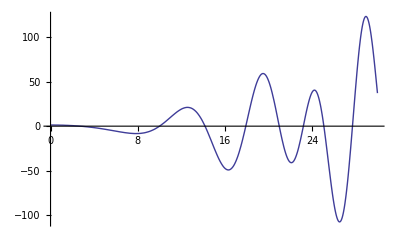

```mathematica
Plot[Re[lz[1000000,s+t I]+lz[1000000,s-t I]/.s->.3],{t,0,30}]
```

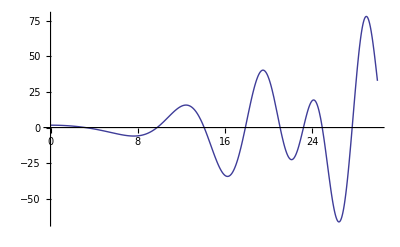

```mathematica
Plot[Re[lz[1000000,1-s+t I]+lz[1000000,1-s-t I]/.s->.3],{t,0,30}]
```

```mathematica
ff[ s_]:=Sum[ ((1-s)/s (j/n)+1)/(j^(s+1)),{j,1,Infinity}]
```

```mathematica
(* *)
```

```mathematica
Expand[s n Zeta[s+1,n+1] - (1-s)(Zeta[s]-Zeta[s,n+1])]
```

```mathematica
N[-Zeta[s]+s Zeta[s]+Zeta[s,1+n]-s Zeta[s,1+n]+n s Zeta[1+s,1+n]/.s->ZetaZero[1]/.n->1000000000000]
```

-2.69036×10^-7+4.18397×10^-7 ⅈ

```mathematica
N[Zeta[s,1+n]-s Zeta[s,1+n]+n s Zeta[1+s,1+n]/.s->3/.n->100000000000000]
```

-4.82047×10^-43

```mathematica
Zeta[s,1+n]-s Zeta[s,1+n]+n s Zeta[1+s,1+n]
```

Zeta[s,1+n]-s Zeta[s,1+n]+n s Zeta[1+s,1+n]

```mathematica
fg[n_,s_]:= s n (Zeta[s+1]-HarmonicNumber[n,s+1])-(1-s)HarmonicNumber[n,s]
fg2[n_,s_]:= (Zeta[s+1]-HarmonicNumber[n,s+1])-(1-s)HarmonicNumber[n,s]/(s n )
fg2a[n_,s_]:= (Zeta[s+1]-HarmonicNumber[n,s+1])
fg2b[n_,s_]:= -(1-s)HarmonicNumber[n,s]/(s n )
```

```mathematica
fg[n,s]/(-(1-s))/.n->100000000000/.s->.5
```

-1.46035

```mathematica
(fg2[n,s]/(-(1-s)))(s n)/.n->100000000000/.s->.5
```

-1.46034

```mathematica
fg2a[n,s]/.n->10000000000/.s->.5
```

0.00002

```mathematica
fe[n_,s_,x_]:=Sum[j^-s,{j,1,n}] - x^(1-s)Sum[j^-s,{j,1,n/x}]
fe2[n_,s_,x_]:=Sum[j^-s,{j,1,n}] - x^(1-s)(Sum[j^-s -(j+n/x)^-s,{j,1,Infinity}])
fe3[n_,s_,x_]:=Sum[j^-s,{j,1,n}] - (Sum[x^(1-s)j^-s -x^(1-s)(j+n/x)^-s,{j,1,Infinity}])
```

```mathematica
N@fe[100000,.5,2]
```

0.603318

```mathematica
N[(1-2^(1-.5))Zeta[.5]]
```

0.604899

```mathematica
N@fe2[100000,.5,2]
```

0.60332

```mathematica
D[x^(1-s)(Sum[j^-s -(j+n/x)^-s,{j,1,Infinity}]),x]/.x->1
```

-n s HurwitzZeta[1+s,1+n]+(1-s) (-HurwitzZeta[s,1+n]+Zeta[s])

```mathematica
D[(Sum[x^(1-s)j^-s -x^(1-s)(j+n/x)^-s,{j,1,Infinity}]),x]/.x->1
```

-n s HurwitzZeta[1+s,1+n]-(1-s) (HurwitzZeta[s,1+n]-Zeta[s])

```mathematica
D[(Sum[ -x^(1-s)(j+n/x)^-s,{j,1,Infinity}]),x]/.x->1
```

-(1-s) HurwitzZeta[s,1+n]-n s HurwitzZeta[1+s,1+n]

```mathematica
D[x^(1-s)j^-s,x]/.x->1
```

j^-s (1-s)

```mathematica
D[-x^(1-s)(j+n/x)^-s,x]/.x->1
```

-(j+n)^-s (1-s)-n (j+n)^(-1-s) s

```mathematica
D[-x^(1-s)aa[n],x]/.x->1
```

-(1-s) aa[n]

```mathematica
D[bb[n](j+n/x)^-s,x]/.x->1
```

n (j+n)^(-1-s) s bb[n]

```mathematica
lt[n_,s_,k_]:=Sum[ n^k/j^(s+k),{j,n+1,Infinity}]
```

```mathematica
N@lt[10,-1,3]
```

95.1663

```mathematica
Sum[ (-1)^k Binomial[t,k] (s+k)/(s-1) n^k / j^(s+k),{k,0,t}]
```

(j^-s (1-n/j)^t (j s-n s-n t))/((j-n) (-1+s))

```mathematica
ad[n_,s_,t_]:= Sum[ j^-s,{j,1,n}]-Sum[ Sum[(-1)^k Binomial[t,k](s-1+k)/(s-1)n^k/j^(s+k),{k,1,t}],{j,n+1,Infinity}]
ad2[n_,s_]:= Sum[ j^-s,{j,1,n}]+(s)/(s-1) Sum[n/j^(s+1),{j,n+1,Infinity}]
```

```mathematica
N@ad[10000,0,3]
```

29999.5

```mathematica
Zeta[.5]
```

-1.46035

```mathematica
(* *)
```

```mathematica
D[(Sum[(-x^(1-s))j^-s -(-x^(1-s))(j+n/x)^-s,{j,1,Infinity}]),{x,2}]/.x->1
```

-2 n s HurwitzZeta[1+s,1+n]+2 n (1-s) s HurwitzZeta[1+s,1+n]+n^2 s (1+s) HurwitzZeta[2+s,1+n]-(1-s) s (HurwitzZeta[s,1+n]-Zeta[s])

```mathematica
D[((-x^(1-s))j^-s),{x,2}]/.x->1
```

j^-s (1-s) s

```mathematica
D[((x^(1-s))(j+n/x)^-s),{x,2}]/.x->1
```

-2 n (j+n)^(-1-s) s-n^2 (j+n)^(-2-s) (-1-s) s+2 n (j+n)^(-1-s) (1-s) s-(j+n)^-s (1-s) s

```mathematica
FullSimplify[-2 n (j+n)^(-1-s) s+2 n (j+n)^(-1-s) (1-s) s]
```

-2 n (j+n)^(-1-s) s^2

```mathematica
ar[n_,s_]:= ((1-s)(s)Sum[j^-s,{j,1,n}] - 2 s^2 Sum[ n/j^(s+1),{j,n+1,Infinity}]+s(s+1)Sum[ n^2/j^(s+2),{j,n+1,Infinity}])/(s(1-s))
arb[n_,s_]:= ((1-s)(s)Sum[j^-s,{j,1,n}] + Sum[- 2 s^2 n/j^(s+1)+s(s+1)n^2/j^(s+2),{j,n+1,Infinity}])/(s(1-s))
```

```mathematica
N@arb[100,-.5]
```

Sum::div: Sum does not converge.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in j near {j} = {8.16907×10^224}. NIntegrate obtained -1.92197089810071×10^13979 and 1.92197089810071×10^13979 for the integral and error estimates.

2.56262786413429×10^13979

```mathematica
Zeta[.5]
```

-1.46035

```mathematica
(* *)
```

```mathematica
D[(Sum[(-x^(1-s))(j+y)^-s -(-x^(1-s))(j+y+n/x)^-s,{j,1,Infinity}]),x]/.x->1
```

-(1-s) (HurwitzZeta[s,1+y]-HurwitzZeta[s,1+n+y])+n s HurwitzZeta[1+s,1+n+y]

```mathematica
D[(-x^(1-s))(j+y)^-s,x]/.x->1
```

-(1-s) (j+y)^-s

```mathematica
D[-(-x^(1-s))(j+y+n/x)^-s,x]/.x->1
```

n s (j+n+y)^(-1-s)+(1-s) (j+n+y)^-s

```mathematica
ax[n_,s_,y_]:=Sum[ (j+y)^-s,{j,1,n}]-s/(s-1) Sum[ n/( j+y)^(-s-1),{j,n+1,Infinity}]
```